```mathematica
(* from RandomAnalyticSignal_Research.nb *)
(* created at 2015/06/14 *)
```

```mathematica
SeedRandom[0]
```

```mathematica
argList[f_,dt_]:=Table[Arg[f[t]],{t,0,2π,dt}];
absList[f_,dt_]:=Table[Abs[f[t]],{t,0,2π,dt}];
reList[f_,dt_]:=Table[Re[f[t]],{t,0,2π,dt}];
correct[li_List]:=Rest[li]+Accumulate[Piecewise[{{-2π,#≥π},{2π,#≤-π}}]&/@Differences[li]];
numberOfExtremum[li_List]:=Length[Select[Differences[li]*RotateRight[Differences[li]],#≤0&]];
inclinationList[f_,dt_]:=Table[Arg[f[t+dt]-c[t]],{t,0,2π,dt}];
breakNumber[li_List]:=Length[Select[Differences[li],#≤-π&]]-Length[Select[Differences[li],#≥π&]] ;
```

```mathematica
normalize[p_,a_,b_]:=If[b-a≠0,(p-a)/(b-a),ComplexInfinity]
cross0Q[x_,y_]:=If[x≠y,IntervalMemberQ[Interval[{x,y}],0],False]intervalIntersectionQ[a_,b_]:=!((a<0&&b<0)||(a>1&&b>1))
complexToVector[x_]:={Re[x],Im[x]}
cross01Q[p2_,q2_]:=If[cross0Q[Im[p2],Im[q2]]&&0≤Re[(Im[p2] q2-Im[q2] p2)/(Im[p2]-Im[q2])]≤1,True,If[Im[p2]==0&&Im[q2]==0,intervalIntersectionQ[Im[p2],Im[q2]],False]]
crossQ[{{p_,q_},{a_,b_}}]:=If[a==b,If[p==q,a==p,cross01Q[normalize[a,p,q],normalize[b,p,q]]],cross01Q[normalize[p,a,b],normalize[q,a,b]]]
curveCrossQ[{{p_,q_},{a_,b_}}]:=If[q≠a&&b≠p,crossQ[{{p,q},{a,b}}],False]
```

```mathematica
lowAmpLi={1,1,1,1,1,0,0,0,0,0};
highAmpLi={0,0,0,0,0,1,1,1,1,1};
```

```mathematica
f[ampLi_List]:=Module[{rotLi=RandomReal[{0,2π},{Length[ampLi]}]},∑_(k=1)^Length[ampLi] ampLi⟦k⟧ Exp[ⅈ k (#-rotLi⟦k⟧)] &];
```

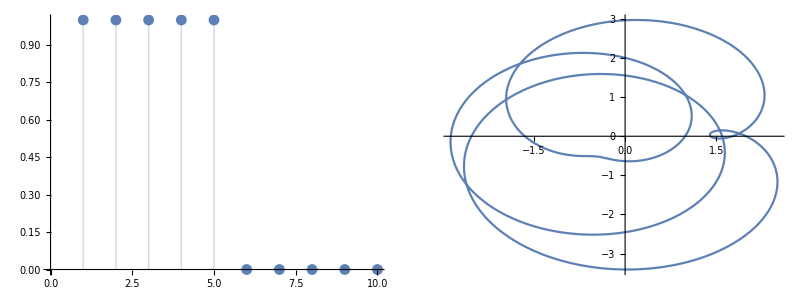

```mathematica
c=f[lowAmpLi];
Grid[{{
ListPlot[lowAmpLi,Filling->Bottom,PlotRange->{0,All}],
ParametricPlot[{Re[#],Im[#]}&[c[t]],{t,0,2π},PlotRange->All]
}}]
```

Rotation:

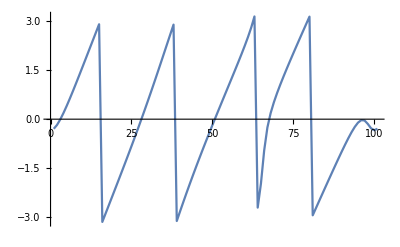

4

```mathematica
(* NumberOfRotation *)
numberOfRotation[f_, dt_]:=breakNumber[inclinationList[f,dt]]
Print["Rotation:"]
ListLinePlot[inclinationList[c,(2π)/100]]
numberOfRotation[c,(2π)/100]
```

ArgExtremum:

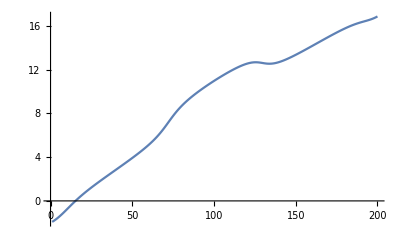

1

```mathematica
(* NumberOfArgExtremum *)
numberOfArgExtremum[f_,dt_]:=numberOfExtremum[correct[argList[f,dt]]]/2;
Print["ArgExtremum:"]
ListLinePlot[correct[argList[c,(2π)/200]]]
numberOfArgExtremum[c,(2π)/200]
```

AbsExtremum:

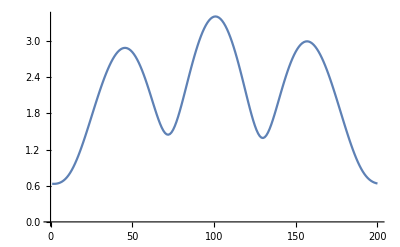

3

```mathematica
(* NumberOfAbsExtremum *)
Print["AbsExtremum:"]
ListLinePlot[correct[absList[c,(2π)/200]]]
numberOfAbsExtremum[f_,dt_]:=numberOfExtremum[correct[absList[f,dt]]]/2
numberOfAbsExtremum[c,(2π)/200]
```

ReExtremum:

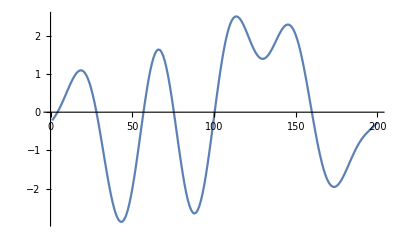

4

```mathematica
(* NumberOfReExtremum *)
Print["ReExtremum:"]
ListLinePlot[correct[reList[c,(2π)/200]]]
numberOfReExtremum[f_,dt_]:=numberOfExtremum[correct[reList[f,dt]]]/2
numberOfReExtremum[c,(2π)/200]
```

```mathematica
(* Sound *)
Play[Re[c[440*2π*t]],{t,0,1}]
```

-Graphics-